```mathematica
"20/07/17"
data = Import["C:\\Users\\Leoleo\\Desktop\\TCC\\Mathematica\\Interpolation\\116.dat"];
```

20/07/17

```mathematica
RCtotal = Table[{data[[i,1]],data[[i,3]]},{i,1,15}];

RCgas = Table[{data[[i,1]],data[[i,4]]},{i,1,15}];
```

```mathematica
Erro = Table[data[[i,5]],{i,1,15}];
```

```mathematica
Needs["ErrorBarPlots`"];
RC =ErrorListPlot[{Table[{RCtotal[[i]],ErrorBar[Erro[[i]]]},{i,15}],Table[{RCgas[[i]],ErrorBar[0]},{i,15}]},Frame->True,PlotLabel->"ESO 116-G12",FrameLabel->{"Raio(Kpc)","Velocidade(Km/s)"}];
```

```mathematica
g = Interpolation[RCgas];
```

```mathematica
Plot[g[x],{x,1,15}];
```

```mathematica
a= Plot[g[x],{x,0.3,11.7},AxesOrigin->{x=0,x=0}];
```

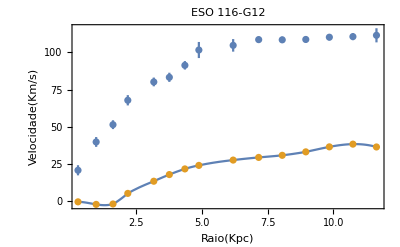

```mathematica
Final = Show[a,RC,Frame->True,PlotRange ->Automatic,  FrameLabel->{"Raio(Kpc)","Velocidade(Km/s)"},PlotLabel->"ESO 116-G12"]
```

```mathematica
"Fórmula Velocidade das estrelas no Disco";
```

```mathematica
"Constante gravitacional em (Kpc/Msol)(Km/s)^2";
"Vdisk é a Velocidade das estrelas no disco AO QUADRADO";
"Md em Massa Solar, valor aproximado";
```

```mathematica
G=4.302*10^-6;
```

```mathematica
Rd= 1.7;
Md= 2.4*10^9;
```

```mathematica
Vdisk[r_]= ((G*Md*(r/Rd)^2)/(2Rd))*(BesselI[0,(r/(2Rd))]*BesselK[0,(r/(2Rd))]-BesselI[1,(r/(2Rd))]BesselK[1,(r/(2Rd))]);
```

```mathematica
c =Plot[Sqrt[Vdisk[r]],{r,0.3,11.7},PlotRange->Automatic];
```

```mathematica
"Tirar o ; para ver o Grafíco";
oo =Show[Final,c];
```

```mathematica
" Fórmula Matéria Escura";
"Ro em Kpc";
Ro=4.3;
Po=45790251.10782867;
```

```mathematica
Vdm[r_]= 6.4*G*(Po*(Ro^3)/r)*(Log[1+(r/Ro)] -ArcTan[r/Ro]+(1/2)*Log[1+(r/Ro)^2]);
```

```mathematica
dm =Plot[Sqrt[Vdm[r]],{r,0.3,11.7},PlotStyle->Dashed];
```

```mathematica
Show[Final,c,dm];
```

```mathematica
"bb,cc são meus parâmetros livres, Eu não consegui fazer o programa achar um bom valor para Po, então eu coloquei o calculado";
```

```mathematica
Vdm2[r_]= 6.4*G*(Po*(bb^3)/r)*(Log[1+(r/Ro)] -ArcTan[r/Ro]+(1/2)*Log[1+(r/Ro)^2]);
```

```mathematica
Vdisk2[r_]= ((G*cc*(r/Rd)^2)/(2Rd))*(BesselI[0,(r/(2Rd))]*BesselK[0,(r/(2Rd))]-BesselI[1,(r/(2Rd))]BesselK[1,(r/(2Rd))]);

Vfinal=Sqrt[Vdisk2[r]+Vdm2[r]];
```

```mathematica
Dmfit=NonlinearModelFit[RCtotal,Vfinal,{bb,cc},r]
```

FittedModel[√(733.463 «1» (BesselI[0,0.294118 r] BesselK[0,0.294118 r]-«1» «1»)+«1»)]

```mathematica
Dmfit["BestFitParameters"]
```

{bb→4.54251,cc→1.67527×10^9}

```mathematica
Dmfitfinal=Plot[Dmfit[r],{r,0.3,11.7}];
```

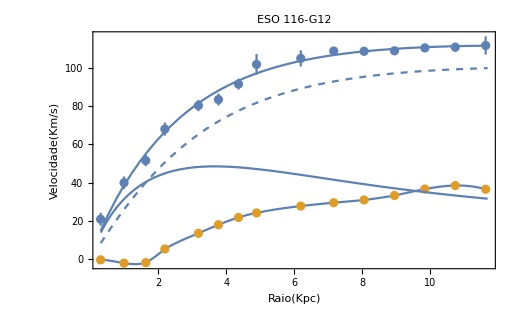

```mathematica
Show[Final,c,dm,ppp]
```